## PHAS2443 Mini-project Decision-making in Committees Hayk Khachatryan - 15013904

## 24/02/2018

```mathematica
Clear[modeler]

modeler[N_, {k_, {h0_, h1_}, e_}] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs:
;	
		N: committee size (N ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

	outputs:
;
		graph probs
*)

Module[
{},

]


modeler::usage = "D[N, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute"
```

D[N, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute

```mathematica
dissensus[n_, sf_, si_] := 
HeavisideTheta[1-Max[sf, n-sf]/n]
```

```mathematica
dissensus[15,3,10]
```

1

```mathematica
Graph[{1 <-> 2, 2<-> 3, 2<-> 4, 1<-> 4}]
```

-Graphics-

### Need to implement the majority update func

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{},

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2) and returns True if at least a majority above the threshold h are agree  *)
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ list

]

]

BooleanConvert[majority[0.6, {a,b,c,d,e}]]
```

(a&&b&&c)||(a&&b&&d)||(a&&b&&e)||(a&&c&&d)||(a&&c&&e)||(a&&d&&e)||(b&&c&&d)||(b&&c&&e)||(b&&d&&e)||(c&&d&&e)

Majority fails to return True for a majority of state 0. This is because BooleanCountingFunction creates a logical statement comparing the elements in the list to each other to see if they’re the same. For a list { a, b, c, d } with h = 0.75, it checks

```mathematica
( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d )
```

(a&&b&&c)||(a&&b&&d)||(b&&c&&d)

While this works when the majority has a state of 1, it fails to work when the majority has a state of 0 (as 0 ∧ 0 ∧ 0 = 0)

```mathematica
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 1, c-> 1, d -> 0}]
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 0, c-> 0, d -> 0}]
```

True

False

```mathematica
Clear[swaps]

swaps[h_, list_, 0] :=
If[majority[h,list],1,0]
swaps[h_,list_, 1] :=
If[majority[h,list], 0, 1]
swaps[h_, list_, e] :=
If[majority[h,list],1,0]
```

## 25/02/2018

Working on a majority function that takes into account  0 ∧ 0 = 0

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{},

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2) and returns True if at least a majority above the threshold h agree *)
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ list

]

]

BooleanConvert[majority[0.6, {a,b,c,d,e}]]
```

(a&&b&&c)||(a&&b&&d)||(a&&b&&e)||(a&&c&&d)||(a&&c&&e)||(a&&d&&e)||(b&&c&&d)||(b&&c&&e)||(b&&d&&e)||(c&&d&&e)

Idea: pass dummy list to BooleanCountingFunction (to get disjunctive form) then swap the elements in the dummy list with our list

```mathematica
h = 0.6
list = {False, False, False, False, True}
l = {0,0,0,0,1}
ab = {a,b,c,d,e}

fdsa = BooleanConvert[
BooleanCountingFunction[
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ Table[bdd i, {i, 1, Length[l]}] ] 


(* then swap the bdd's back with rules *)
```

0.6

{False,False,False,False,True}

{0,0,0,0,1}

{a,b,c,d,e}

(bdd&&2 bdd&&3 bdd)||(bdd&&2 bdd&&4 bdd)||(bdd&&2 bdd&&5 bdd)||(bdd&&3 bdd&&4 bdd)||(bdd&&3 bdd&&5 bdd)||(bdd&&4 bdd&&5 bdd)||(2 bdd&&3 bdd&&4 bdd)||(2 bdd&&3 bdd&&5 bdd)||(2 bdd&&4 bdd&&5 bdd)||(3 bdd&&4 bdd&&5 bdd)

Small break from figuring out majority, playing around with cellular automata

(0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

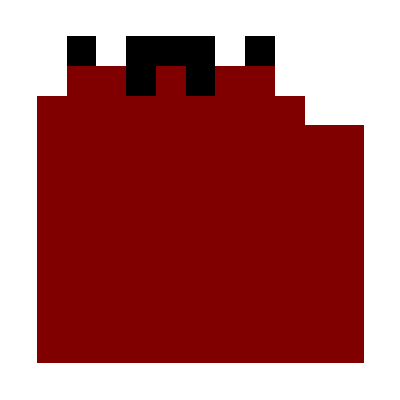

```mathematica
up[lst_,t_]:=BooleanConvert[majority[0.8,lst]]


With[
{
init={0,1,0,1,1,1,0,1,0,0,0},
nsteps=10,
r=2
},
res=CellularAutomaton[{up,{},r},init,nsteps]
];
MatrixForm[res] //. {0 -> False, 1-> True} //. {False -> 0, True -> 1}

ArrayPlot[res]
```

## 26/02/2018

Finish implementing dummy list

```mathematica
h = 0.6
list = {False, False, False, False, True}
l = {0,0,0,0,1}
abList =  Table[bdd i, {i, 1, Length[l]}] 

fdsa = BooleanConvert[
BooleanCountingFunction[
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ abList]


fdsa //. Table[abList[[i]] -> l[[i]], {i, 1, Length[l]}] //. {And -> Equal}
```

0.6

{False,False,False,False,True}

{0,0,0,0,1}

{bdd,2 bdd,3 bdd,4 bdd,5 bdd}

(bdd&&2 bdd&&3 bdd)||(bdd&&2 bdd&&4 bdd)||(bdd&&2 bdd&&5 bdd)||(bdd&&3 bdd&&4 bdd)||(bdd&&3 bdd&&5 bdd)||(bdd&&4 bdd&&5 bdd)||(2 bdd&&3 bdd&&4 bdd)||(2 bdd&&3 bdd&&5 bdd)||(2 bdd&&4 bdd&&5 bdd)||(3 bdd&&4 bdd&&5 bdd)

True

Success! Now to implement it into majority[h, list]

```mathematica
Clear[majority, stringer]

stringer[i_] := ToString[ab]<>ToString[i] (* creates a value "abi" for dummy variables in majority *)

majority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{
ab = Table[stringer[i], {i, 1, Length[list]}]  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
},

swaps =  Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]

majority[0.9, {0,0,0,0,0,0,0,0,0,1}]
```

True